## Analytical Slope by WD: f_1,g_1

```mathematica
Clear["Global`*"]
(* This ODE system corresponds to PG2 with anzats z=x-ct *)
odeP=c*P'[z]+α*P[z]*(1-P[z]-M[z])-(qm+μ)*P[z]+qp*M[z];
odeM=c*M'[z]+Dv*M''[z]-qp*M[z]+qm*P[z];
(* We let ξ=ᾱ z. => P[z_]=f[ξ[z]]; M[z_]=g[ξ[z]]; etc
 We look for solutions of the following form *)
f[ξ_]=Subscript[f, 0][ξ]+ᾱ*Subscript[f, 1][ξ]+1/2*ᾱ^2*Subscript[f, 2][ξ];
g[ξ_]=Subscript[g, 0][ξ]+ᾱ*Subscript[g, 1][ξ]+1/2*ᾱ^2*Subscript[g, 2][ξ];
(* new system is derived by hand by hand*)
Print["---------- New ODE system -------------------"]
odeP=ᾱ*c*f'[ξ]+ᾱ*f[ξ]-α*f[ξ]*(f[ξ]+g[ξ])-qm*f[ξ]+qp*g[ξ];
odeM=ᾱ*c*g'[ξ]+ᾱ^2*Dv*g''[ξ]-qp*g[ξ]+qm*f[ξ];
odeP==0
odeM==0
Print["---------- Finding coefficients of ᾱ -------------------"]
coeffP=CoefficientList[odeP,ᾱ]
coeffM=CoefficientList[odeM,ᾱ]
Print["----------O(1)==0--------------"]
coeffM[[1]]==0
coeffP[[1]]==0
Solve[{coeffP[[1]]==0,coeffM[[1]]==0},{Subscript[f, 0][ξ],Subscript[g, 0][ξ]}]
Print["----------O(ᾱ)==0--------------"]
Subscript[f, 0][ξ_]=0; Subscript[g, 0][ξ_]=0; (* Result from O(1)==0 *)
coeffM[[2]]==0
coeffP[[2]]==0
Solve[{coeffP[[2]]==0,coeffM[[2]]==0},{Subscript[f, 1][ξ],Subscript[g, 1][ξ]}]
Print["----------O(ᾱ^2)==0--------------"]
Subscript[g, 1][ξ_]=qm *Subscript[f, 1][ξ]/qp; (* Result from O(ᾱ)==0 *)
coeffM[[3]]==0
coeffP[[3]]==0
Print["----------O(ᾱ^2)==0--------Solving DE------"]
de=Simplify[coeffP[[3]]+coeffM[[3]]]
Solve[de==0,Subscript[f, 1]'[ξ]]
Simplify[DSolve[{de==0,Subscript[f, 1][0]==1/(2*α)/(1+qm/qp)},Subscript[f, 1][ξ],ξ]]


Quit[](* Clear ALL definitions, including functions*)
```

---------- New ODE system -------------------

-qm (f_0[ξ]+ᾱ f_1[ξ]+1/2 (ᾱ)^2 f_2[ξ])+ᾱ (f_0[ξ]+ᾱ f_1[ξ]+1/2 (ᾱ)^2 f_2[ξ])+qp (g_0[ξ]+ᾱ g_1[ξ]+1/2 (ᾱ)^2 g_2[ξ])-α (f_0[ξ]+ᾱ f_1[ξ]+1/2 (ᾱ)^2 f_2[ξ]) (f_0[ξ]+ᾱ f_1[ξ]+1/2 (ᾱ)^2 f_2[ξ]+g_0[ξ]+ᾱ g_1[ξ]+1/2 (ᾱ)^2 g_2[ξ])+c ᾱ (f_0'[ξ]+ᾱ f_1'[ξ]+1/2 (ᾱ)^2 f_2'[ξ])==0

qm (f_0[ξ]+ᾱ f_1[ξ]+1/2 (ᾱ)^2 f_2[ξ])-qp (g_0[ξ]+ᾱ g_1[ξ]+1/2 (ᾱ)^2 g_2[ξ])+c ᾱ (g_0'[ξ]+ᾱ g_1'[ξ]+1/2 (ᾱ)^2 g_2'[ξ])+Dv (ᾱ)^2 (g_0''[ξ]+ᾱ g_1''[ξ]+1/2 (ᾱ)^2 g_2''[ξ])==0

---------- Finding coefficients of ᾱ -------------------

{-qm f_0[ξ]-α f_0[ξ]^2+qp g_0[ξ]-α f_0[ξ] g_0[ξ],f_0[ξ]-qm f_1[ξ]-2 α f_0[ξ] f_1[ξ]-α f_1[ξ] g_0[ξ]+qp g_1[ξ]-α f_0[ξ] g_1[ξ]+c f_0'[ξ],f_1[ξ]-α f_1[ξ]^2-1/2 qm f_2[ξ]-α f_0[ξ] f_2[ξ]-1/2 α f_2[ξ] g_0[ξ]-α f_1[ξ] g_1[ξ]+1/2 qp g_2[ξ]-1/2 α f_0[ξ] g_2[ξ]+c f_1'[ξ],f_2[ξ]/2-α f_1[ξ] f_2[ξ]-1/2 α f_2[ξ] g_1[ξ]-1/2 α f_1[ξ] g_2[ξ]+1/2 c f_2'[ξ],-1/4 α f_2[ξ]^2-1/4 α f_2[ξ] g_2[ξ]}

{qm f_0[ξ]-qp g_0[ξ],qm f_1[ξ]-qp g_1[ξ]+c g_0'[ξ],1/2 qm f_2[ξ]-1/2 qp g_2[ξ]+c g_1'[ξ]+Dv g_0''[ξ],1/2 c g_2'[ξ]+Dv g_1''[ξ],1/2 Dv g_2''[ξ]}

----------O(1)==0--------------

qm f_0[ξ]-qp g_0[ξ]==0

-qm f_0[ξ]-α f_0[ξ]^2+qp g_0[ξ]-α f_0[ξ] g_0[ξ]==0

{{f_0[ξ]→0,g_0[ξ]→0}}

----------O(ᾱ)==0--------------

qm f_1[ξ]-qp g_1[ξ]==0

-qm f_1[ξ]+qp g_1[ξ]==0

Solve::svars: Equations may not give solutions for all "solve" variables.

{{g_1[ξ]→(qm f_1[ξ])/qp}}

----------O(ᾱ^2)==0--------------

1/2 qm f_2[ξ]-1/2 qp g_2[ξ]+(c qm f_1'[ξ])/qp==0

f_1[ξ]-α f_1[ξ]^2-(qm α f_1[ξ]^2)/qp-1/2 qm f_2[ξ]+1/2 qp g_2[ξ]+c f_1'[ξ]==0

----------O(ᾱ^2)==0--------Solving DE------

(qp f_1[ξ]-(qm+qp) α f_1[ξ]^2+c (qm+qp) f_1'[ξ])/qp

{{f_1'[ξ]→(-qp f_1[ξ]+qm α f_1[ξ]^2+qp α f_1[ξ]^2)/(c (qm+qp))}}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{f_1[ξ]→qp/((1+ⅇ^((qp ξ)/(c (qm+qp)))) (qm+qp) α)}}

### Approximate analytical solution expression

```mathematica
Subscript[f, 1][ξ_]=qp/((1+ⅇ^((qp ξ)/(c (qm+qp)))) (qm+qp) α);
Subscript[g, 1][ξ_]=qm/qp*Subscript[f, 1][ξ];
dens[ξ_]=ᾱ*(Subscript[f, 1][ξ]+Subscript[g, 1][ξ]);
dens[z_]=Simplify[dens[ᾱ*z] ](* Since ξ=ᾱ*z *)
Quit[]
```

(ᾱ)/(α+ⅇ^((qp z ᾱ)/(c (qm+qp))) α)

### Approximate analytical slope expression

```mathematica
Subscript[f, 1][ξ_]=qp/((1+ⅇ^((qp ξ)/(c (qm+qp)))) (qm+qp) α);
Subscript[g, 1][ξ_]=qm/qp*Subscript[f, 1][ξ];
dens[ξ_]=ᾱ*(Subscript[f, 1][ξ]+Subscript[g, 1][ξ]);
dens[z_]=Simplify[dens[ᾱ*z] ];(* Since ξ=ᾱ*z *)
densPrime[z_]=dens'[z];
slope=-densPrime[0]
Quit[]
```

(qp (ᾱ)^2)/(4 c (qm+qp) α)

### Testing parameters for solution plot

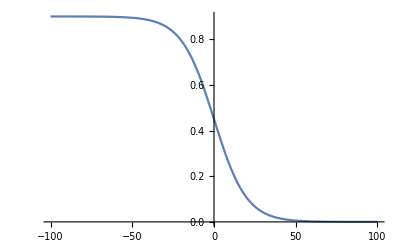

0.45

```mathematica
dens[z_]=(ᾱ)/(α+ⅇ^((qp z ᾱ)/(c (qm+qp))) α);
α=1;
Dv=25;
qp=20;
qm=20;
μ=0.1;
ᾱ=α-μ;
c=4.74342;

Plot[dens[z],{z,-100,100}]
dens[0] (*Should equal 1/2*(1-μ/α)*)
Quit[]
```

### Testing parameters for slope plot

(qp (ᾱ)^2)/(4 c (qm+qp) α)

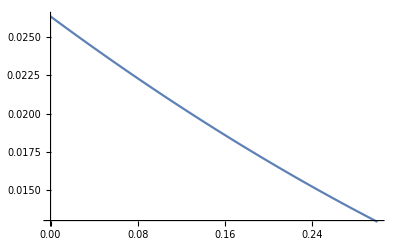

```mathematica
slope=(qp (ᾱ)^2)/(4 c (qm+qp) α)
α=1;
Dv=25;
qp=20;
qm=20;
(*μ=0.1;*)
ᾱ=α-μ;
c=4.74342;

Plot[slope,{μ,0,0.3}]
Quit[]
```

## Slope_2 by WOS

-(16 qp (α-μ))/(25 c (qm+qp) (Log[(α-5 μ)/(4 α)]-Log[21/4-(25 μ)/(4 α)]))

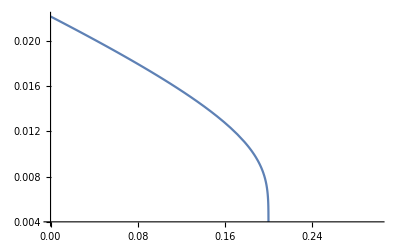

```mathematica
dens[z_]=(ᾱ)/(α+ⅇ^((qp z ᾱ)/(c (qm+qp))) α);
(* zx[x_]=Solve[dens[z]==x,z]*) (* Why is this fucking with me? *)
zx[x_]=Log[(α-μ)/(x*α)-1]*c*(qp+qm)/(qp*(α-μ));
slope2=-Simplify[(4/25-4/5)/(zx[4/25]-zx[4/5])]

α=1;
Dv=25;
qp=20;
qm=20;
(*μ=0.1;*)
c=4.74342;

Plot[slope2,{μ,0,0.3}]


Quit[]
```

### Testing slope_2

```mathematica
Dv=72/365;
qp=20;
qm=20;
cdata=0.03534; (* From data *)
sdata=0.36826; (* From data *)

(*
Why must i have abs of slope to get a reasonable(positive) mu?

*)
slope2=Abs[-(16 qp (α-μ))/(25 c (qm+qp) Log[(α-5 μ)/(21α-25μ)])];
c=Sqrt[Dv*(α-μ)/(1-(α-μ)/(3*qp))];

Solve[{c==cdata,slope2==sdata},{α,μ}]

Quit[]
```

{{α→-0.180019,μ→-0.18635},{α→0.227499,μ→0.221168}}